# How Genotype-by-Environment Interactions can maintain variation in mutualisms - mathematical supplement and simulations.

## Setup:

Clear kernel of unwanted junk!

```mathematica
(*Quit[]*)
```

Setup dynamical expressions. First, I start by determining the average payoff advantage of each host and symbiont phenotype in each environment. Here, we use a change of parameters, where parameters in these expressions are the advantage of genotype 1 over genotype 2 when partnering with a given partner genotype. These can be translated into the contributions of G, GXG, GXE, and GXGXE to fitness where ΔW/V11 = μ_x + δ_x+ ϵ_x+γ_x,  ΔW/V22 = μ_x -δ_x- ϵ_x-γ_x  ΔW/V21 = μ_x +δ_x- ϵ_x  and ΔW/V12 = μ_x +ϵ_x-δ_x.

```mathematica
ΔW1S1=s1* ΔW11+(1-s1) ΔW12;
ΔW2S2=s2* ΔW21+(1-s2) ΔW22;
ΔV1H1=h1* ΔV11+(1-h1) ΔV12;
ΔV2H2=h2* ΔV21+(1-h2) ΔV22;
```

Frequency of each strategist in each patch and allow dispersal between the patches:

```mathematica
H1d=h1*(1-h1)*(ΔW1S1)+dh*h2-dh*h1;
H2d= h2*(1-h2)*(ΔW2S2)-dh*h2+dh*h1;
S1d=s1*(1-s1)*(ΔV1H1)+ds*s2-ds*s1;
S2d=s2*(1-s2)*(ΔV2H2)-ds*s2+ds*s1;
```

Change of variables to decomposition:

```mathematica
cov= {ΔW11 -> δh+ϵh+γh+μh, ΔW12 -> -δh+ϵh+μh,ΔW21-> δh-ϵh+μh, ΔW22 ->- δh-ϵh-γh+μh,ΔV11 -> δs+ϵs+γs+μs, ΔV12 ->- δs+ϵs+μs,ΔV21-> δs-ϵs+μs, ΔV22 ->- δs-ϵs-γs+μs};
```

## Finding Boundary Equilibria:

Build jacobian and try boundaries:

```mathematica
J=Simplify[{
{D[H1d, h1],D[H2d,h1],D[S1d,h1],D[S2d,h1]},{D[H1d, h2],D[H2d,h2],D[S1d,h2],D[S2d,h2]},{D[H1d, s1],D[H2d,s1],D[S1d,s1],D[S2d,s1]},{D[H1d, s2],D[H2d,s2],D[S1d,s2],D[S2d,s2]}}];
candidates=Tuples[{0,1},4];(*can also plug in candidates from no dispersal case to get same results. *)
(*Evaluate equations at candidates from no dispersal case and return those that are equilibria. *)
equilibrialist={};
Do[{eval={H1d,H2d,S1d,S2d}/. {h1->candidates[[i,1]],h2->1candidates[[i,2]],s1->candidates[[i,3]], s2->candidates[[i,4]]},If[eval=={0,0,0,0},AppendTo[equilibrialist,candidates[[i]]]]}
,{i,1,Length[candidates]}]
equilibrialist
```

```mathematica
J//MatrixForm//Factor
```

(h1e1,h1e2,s1e1,s1e2)
So there are only two sets of boundary equilibria. One where one genotype fixes everywhere,
 and another when genotypes and environments mismatch.

Let’s evaluate the Jacobian for the mismatching environment, matching genotype equilibrium:

```mathematica
J/.{h1-> 1,s1-> 1,h2-> 1,s2-> 1}//MatrixForm
(*The matrices are in block diagonal form, and the block diagonals of each equilbrium are symmetric. *)
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = %%[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]//Simplify
a2=%%[[1]]//Simplify
```

```mathematica
J/.{h1-> 0,s1-> 0,h2-> 0,s2-> 0}
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = %%[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]//Simplify
a2=%%[[1]]//Simplify
```

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r];
CoefficientList[%,r];
a1=%[[2]]//Simplify
a2=%%[[1]]//Simplify
```

```mathematica
J/.{h1-> 0,h2-> 0,s1-> 1,s2-> 1}//MatrixForm
J/.{h1-> 1,h2-> 1,s1-> 0,s2-> 0}//MatrixForm
(*The matrices are in block diagonal form, and the block diagonals of each equilbrium are symmetric. *)
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = %%[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r];
CoefficientList[%,r];
a1h=%[[2]]//Simplify
a2h=%%[[1]]//Simplify
```

```mathematica
a2h/.cov//Simplify
```

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r];
CoefficientList[%,r];
a1s=%[[2]]//Simplify
a2s=%%[[1]]//FullSimplify
```

## Approximating Internal Equilibria - both rates of dispersal are small.

```mathematica
assumptionfn[x_] := x/.{ds-> ds*ϵ,dh-> dh*ϵ,h1->h10+ h11*ϵ,h2-> h20+h21*ϵ,s1->s10+s11* ϵ, s2->s20+s21* ϵ};
{H1d,H2d,S1d,S2d}//assumptionfn//Factor;
Series[%,{ϵ,0,0}]//Normal(*0th Order Approximation*);
ans=Solve[%==0,{h10,h20,s10,s20}]//FullSimplify
```

```mathematica
ApproximatedEq={};
Do[{sys={H1d,H2d,S1d,S2d}//assumptionfn//Factor;
exp=Series[sys,{ϵ,0,1}]//Normal(*First Order Approximation*);
eval=exp/.ans[[i]]//Factor;
firstorder=Solve[eval==0,{h11,h21,s11,s21}]//Factor;
approximated={};
Do[eqi=ans[[ i,j,2]]+firstorder[[1,j,2]];
AppendTo[approximated,eqi],{j,1,4}];
AppendTo[ApproximatedEq,approximated]},{i,1,Length[ans]}]
```

```mathematica
ApproximatedEq;
```

Approximate 0th order values of eigenvalues with weak dispersal for all candidate approximated equilibria:

```mathematica
Othorderterms=Table[{JC = J/.{h1->ApproximatedEq[[i,1]],h2-> ApproximatedEq[[i,2]],s1-> ApproximatedEq[[i,3]],s2->ApproximatedEq[[i,4]]}/.{ds->ds ϵ,dh-> dh*ϵ};
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0][[All,1,2]]//Factor,i}
,{i,1,Length[ApproximatedEq]}]
```

Filter out equilibria that are unstable to 0th order (i.e., one or more approximated eigenvalue is positive) using the assumption that ΔW11 and ΔV11 are positive and ΔW22 and ΔV22 are negative. Much of this was done by hand. We often leverage that 0th order stability criteria are identical except being of opposite sign and thus if one is negative the other is necessarily positive.

```mathematica
unstables={1,2,3,4,6,7,8,9,11,12,13,14,16,17,18,19,21,22,23,24,25};(*List of equilibria that must be unstable*)
filteredeq={};
Do[If[ContainsAny[{i},unstables]==False,AppendTo[filteredeq,ApproximatedEq[[i]]]],{i,1,Length[ApproximatedEq]}]
```

Write a function that carries out the remaining perturbation analysis to approximate stability to the first order:

```mathematica
StabilityofEQ[EQ_]:={
EQ//Simplify,
JC = J/.{h1->EQ[[1]],h2-> EQ[[2]],s1-> EQ[[3]],s2->EQ[[4]]}/.{ds->ds ϵ,dh-> dh*ϵ};
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor;
Othorderλs,
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstsp=Table[{
λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,4}];
unsolvedfirstO=Table[{
λ11=a/.Othorderλs[[i]]//Chop//Factor},{i,1,4}];
firsts=firstsp//Flatten;
firsts//Factor//FullSimplify,
approximatedeigval=Othorderλs[[1;;4,1,2]]+firsts[[1;;4,2]]//Factor}
```

```mathematica
Length[filteredeq]
```

### First equilibrium global genotypic match:

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[1]] ]
```

```mathematica
Oth
```

This equilibrium will be stable when approximated to the 0th

```mathematica
Oth/.cov
```

### Second Candidate (Migration-Selection Balance):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[2]] ]
```

```mathematica
eq
```

```mathematica
Oth
```

This equilibrium is always valid and stable under our approximation because we assume ΔW/V11 > 0 and ΔW/V22 <0 .

```mathematica
{eq,Oth}/.cov
```

### Third Candidate (Reverse Migration-Selection Balance):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[3]] ]
```

```mathematica
eq
Oth
{eq,Oth}/.cov
```

This equilibrium is valid and stable when ΔW/V12 <0 and ΔW/V21>0.

### Fourth Candidate (global genotypic match):

```mathematica
{eq,Oth,first,total}=StabilityofEQ[ filteredeq[[4]]]
{eq,Oth}/.cov
```

This equilibrium is also stable when dispersal is rare.

## Simulations of Single Trajectories (symmetric dispersal):

```mathematica
dynsys[h10_,h20_,s10_,s20_,ΔW11_,ΔW21_,ΔV11_,ΔV21_]:= {
h1'[t]==-dh h1[t]+dh h2[t]+(1-h1[t]) h1[t] (s1[t] ΔW11+(1-s1[t]) ΔW12),h2'[t]==dh h1[t]-dh h2[t]+(1-h2[t]) h2[t] (s2[t] ΔW21+(1-s2[t]) ΔW22),s1'[t]==-ds s1[t]+ds s2[t]+(1-s1[t]) s1[t] (h1[t] ΔV11+(1-h1[t]) ΔV12),s2'[t]==ds s1[t]-ds s2[t]+(1-s2[t]) s2[t] (h2[t] ΔV21+(1-h2[t]) ΔV22),h1[0]==h10,h2[0]==h20,s1[0]==s10,s2[0]==s20}/.{ΔW22 -> -ΔW11,ΔW12-> -ΔW21,ΔV22 -> -ΔV11,ΔV12-> -ΔV21,ds-> dh}
```

#### Solve parametrically and vary dispersal:

Example trajectories when ΔW/V11 + ΔW/V21 >0 but there’s a local fitness disadvantage in one environment:

```mathematica
dynsol=ParametricNDSolveValue[dynsys[0.5,0.59,0.41,0.5,2,-1.9,2,-1.9],{h1[t],h2[t],s1[t],s2[t]},{t,0,50},{dh}];
```

Try out some values of dispersal:

```mathematica
fxntable=Table[{di,dynsol[di]},{di,0,0.8,0.1}];
h1e1v=fxntable[[All,2,1]];
h1e2v=fxntable[[All,2,2]];
cols=fxntable[[All,1]];
stratlist={"h1","h2"};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
```

```mathematica
aestable=Table[{linelist[[i]],ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{i,1,Length[stratlist]},{j,1,Length[cols]}]~Flatten~1;
```

```mathematica
Legended[Plot[{h1e1v,h1e2v},{t,0,50},PlotRange->{-0.1,1.1},PlotStyle->aestable,PlotLegends-> cols ], LineLegend[{linelist[[1]],linelist[[2]]},stratlist]]
```

Example trajectories when ΔW/V11 + ΔW/V21 >0 and ΔW/V11 = -ΔW/V22 and  ΔW/V21 =  -ΔW/V12.

```mathematica
(*dynsys[h10_,h20_,s10_,s20_,ΔW11_,ΔW21_,ΔV11_,ΔV21_]*)dynsol=ParametricNDSolveValue[dynsys[h0,h0,s0,s0,0.1,-0.7,0.1,-0.7],{h1[t],h2[t],s1[t],s2[t]},{t,0,500},{dh,h0,s0}]
```

```mathematica
fxntable=Table[{{di,h0},dynsol[di,h0,s0]},{di,{0.05,0.15}},{h0,{0.5,0.75}},{s0,{0.5}}];
fxntable2=Flatten[fxntable,2];
h1e1v=fxntable2[[All,2,1]];
h1e2v=fxntable2[[All,2,2]];
s1e1v=fxntable2[[All,2,3]];
s1e2v=fxntable2[[All,2,4]];
cols=fxntable2[[All,1]];
stratlist={"h1e1","h1e2"};
dlist={0.05,0.15};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]]},{i,1,Length[linelist]}]~Flatten~1;
myplot=Legended[Plot[{h1e1v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Red,Thick,Dashed},{Red,Thick},{Blue,Thick,Dashed},{Blue,Thick}},AxesLabel->{"time","Frequency"},PlotLabel-> "h_1",AxesStyle->Thick,LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black} ,ImageSize->Large], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate",LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black}]]
(*Export["host1plot.png",myplot];*)
```

```mathematica
host2plot=Legended[Plot[{h1e2v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Red,Thick,Dashed},{Red,Thick},{Blue,Thick,Dashed},{Blue,Thick}},AxesLabel->{"time","Frequency"},PlotLabel-> "h_2",AxesStyle->Thick,LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black} ,ImageSize->Large ], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate"]]
(*Export["host2plot.png",host2plot]*)
```

```mathematica
Legended[Plot[{s1e1v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e1" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

```mathematica
Legended[Plot[{s1e2v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e2" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

## Numerical Simulations of Many Trajectories (symmetric dispersal) :

### Functions for simulation analysis:

A function that plots final frequencies of hosts and symbionts after 10000 units of time.

```mathematica
dynsys[h10_,h20_,s10_,s20_,ΔW11_,ΔW21_,ΔV11_,ΔV21_]:= {
h1'[t]==-dh h1[t]+dh h2[t]+(1-h1[t]) h1[t] (s1[t] ΔW11+(1-s1[t]) ΔW12),h2'[t]==dh h1[t]-dh h2[t]+(1-h2[t]) h2[t] (s2[t] ΔW21+(1-s2[t]) ΔW22),s1'[t]==-ds s1[t]+ds s2[t]+(1-s1[t]) s1[t] (h1[t] ΔV11+(1-h1[t]) ΔV12),s2'[t]==ds s1[t]-ds s2[t]+(1-s2[t]) s2[t] (h2[t] ΔV21+(1-h2[t]) ΔV22),h1[0]==h10,h2[0]==h20,s1[0]==s10,s2[0]==s20}/.{ΔW22 -> -ΔW11,ΔW12-> -ΔW21,ΔV22 -> -ΔV11,ΔV12-> -ΔV21,ds-> dh}/.dh-> d

PlotWFN[h10_,h20_,s10_,s20_,ΔW11_,ΔW21_,ΔV11_,ΔV21_,dmax_,deltad_]:={tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[h10,h20,s10,s20,ΔW11,ΔW21,ΔV11,ΔV21],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{d,h10},AccuracyGoal->5,PrecisionGoal->3];
(*Solve dynamical system and store the final value of the frequency of each symbiont at time tmax for each initial frequency that is imputed to the function. *)
fxntable2=Table[{d,h10,dynsol[d,h10]},{h10,0,1,0.01},{d,0,dmax,deltad}]~Flatten~1;
dlist=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
s1e1v=fxntable2[[All,3,3]];
s1e2v=fxntable2[[All,3,4]];
h1e1p=Transpose@{dlist,averagef,h1e1v};
h1e2p=Transpose@{dlist,averagef,h1e2v};
s1e1p=Transpose@{dlist,averagef,s1e1v};
s1e2p=Transpose@{dlist,averagef,s1e2v};
(*Transform tables of final frequencies for plotting.  *)
stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h2",h1e2p},{"s2",s1e2p}};
plotlist={};
(*Plot final frequency of each host and symbiont*)
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-deltad,dmax+deltad},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#FFFFFF"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];
Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#FFFFFF"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]
}
```

Here, let’s compare the fitness advantage across environments using an additional function that compares fitness within and between environments:

```mathematica
fitnessfxn3[ΔW11_,ΔW21_,ΔV11_,ΔV21_]:=
{w1=s1 *ΔW11+(1-s1)* ΔW12/.{ΔW22 -> -ΔW11,ΔW12-> -ΔW21,ΔV22 -> -ΔV11,ΔV12-> -ΔV21};
w2=s1* ΔW21+(1-s1) ΔW22/.{ΔW22 -> -ΔW11,ΔW12-> -ΔW21,ΔV22 -> -ΔV11,ΔV12-> -ΔV21};
Plot[{w1,w2,Mean[{w1,w2}]},{s1,0,1},AxesLabel->{" ","Host 1 fitness"},PlotLabel-> "Host 1 local fitness advantage",AxesStyle -> Thick, PlotLabels->{"Env. 1","Env. 2","Mean"},LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},PlotStyle->{Thick},TicksStyle-> Directive[Large],ImageSize->Large],
averageΔWg1=Table[{s1,s2,w1=s1 ΔW11+(1-s1) ΔW12/.{ΔW22 -> -ΔW11,ΔW12-> -ΔW21,ΔV22 -> -ΔV11,ΔV12-> -ΔV21};w2=s2 ΔW21+(1-s2) ΔW22/.{ΔW22 -> -ΔW11,ΔW12-> -ΔW21,ΔV22 -> -ΔV11,ΔV12-> -ΔV21};Mean[{w1,w2}]},{s1, 0,1,0.01},{s2,0,1,0.01}];
averageΔWg1p=Flatten[averageΔWg1,1];
ListDensityPlot[averageΔWg1p,Frame->True,FrameLabel->{"s_1","s_2"},LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large],PlotRange->{{-0.01,1.01},{-0.01,1.01},All},AspectRatio->1,ColorFunction-> "BlueGreenYellow",InterpolationOrder-> 0,PlotLabel-> "Host 1 average global fitness advantage",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{Min[averageΔWg1p[[All,3]]],Max[averageΔWg1p[[All,3]]]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Global average fitness advantage"],Right],ImageSize->Large]
}
```

Function for plotting several different initial conditions in the same plot. In the top panel hosts and symbionts increase in sync, while in the bottom as global host frequency increases, symbiont frequency decreases:

```mathematica
PlotWFN3[ΔW11_,ΔW21_,ΔV11_,ΔV21_,dmax_]:={
tmax=10000;
(*dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)(*IC's for GM*)
dynsol=ParametricNDSolveValue[dynsys[h10,h10,h10,h10,ΔW11,ΔW21,ΔV11,ΔV21],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{d,h10},AccuracyGoal->3,PrecisionGoal->3];
fxntableGM=Table[{d,h10,dynsol[d,h10]},{h10,0,1,0.01},{d,0,dmax,dmax/50}]~Flatten~1;
(*dispersal values:*)
dlist=fxntableGM[[All,1]];

(*frequencies: *)
averagef=fxntableGM[[All,2]];
h1e1GM=Transpose@{dlist,averagef,fxntableGM[[All,3,1]]};
s1e1GM=Transpose@{dlist,averagef,fxntableGM[[All,3,3]]};

(*IC's for GMM*)
dynsol=ParametricNDSolveValue[dynsys[h10,h10,(1-h10),(1-h10),ΔW11,ΔW21,ΔV11,ΔV21],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{d,h10},AccuracyGoal->3,PrecisionGoal->3];
fxntableGMM=Table[{d,h10,dynsol[d,h10]},{h10,0,1,0.01},{d,0,dmax,dmax/50}]~Flatten~1;
h1e1GMM=Transpose@{dlist,averagef,fxntableGMM[[All,3,1]]};
s1e1GMM=Transpose@{dlist,averagef,fxntableGMM[[All,3,3]]};


(*IC's for Mig-sel balance and reverse mig-sel balance*)
dynsol=ParametricNDSolveValue[dynsys[h10,(1-h10),h10,(1-h10),ΔW11,ΔW21,ΔV11,ΔV21],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{d,h10},AccuracyGoal->3,PrecisionGoal->3];
fxntableMSB=Table[{d,h10,dynsol[d,h10]},{h10,0,1,0.01},{d,0,dmax,dmax/50}]~Flatten~1;
h1e1MSB=Transpose@{dlist,averagef,fxntableMSB[[All,3,1]]};
s1e1MSB=Transpose@{dlist,averagef,fxntableMSB[[All,3,3]]};

stratlist={{"h_1",h1e1GM},{"s_1",s1e1GM},{"h_1",h1e1GMM},{"s_1",s1e1GMM},{"h_1",h1e1MSB},{"s_1",s1e1MSB}};
lablist={"a)","b)","c)","d)","e)","f)"};
plotlist={};
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-dmax/25,dmax+dmax/25},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction->(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 56+10],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 38+10],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->{{125,25},{100,150}}
,PlotRangeClipping->False
 ,Epilog->Inset[Style[lablist[[i]],Directive[FontSize-> 56+10],FontFamily->"Times",FontColor-> Black],(*Offset[{-1,-1},Scaled[{1,1}]],*)Scaled[{-0.05,1.10}]]]],{i,1,Length[stratlist]}];

Legended[Labeled[Grid[{{Style["Initially near global genotypic match equilibria ",66,FontFamily->"Times",FontColor->Black],SpanFromLeft},{plotlist[[1]],plotlist[[2]]},{Style["Initially near global genotypic mismatch equilibria",66,FontFamily->"Times",FontColor->Black],SpanFromLeft},{plotlist[[3]],plotlist[[4]]},{Style["Initially near internal equilibria",66,FontFamily->"Times",FontColor->Black],SpanFromLeft},{plotlist[[5]],plotlist[[6]]}},ItemSize->Full,Spacings->Scaled[0.05] ] (*,Epilog->Inset[Style["h1 = h2 = s1 = s2",Directive[FontSize-> 56+f],FontFamily->"Times",FontColor-> Black,Bold],(*Offset[{-1,-1},Scaled[{1,1}]],*)Scaled[{0.5,0.5}]]*)
,

{"Initial frequency","Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 90+10,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{50,50},{50,50}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->Style["Final frequency",62,FontFamily->"Times"],LegendMarkerSize->{80,900} ,LabelStyle -> {FontSize-> 38+10,FontFamily->"Times",FontColor-> Black}],Right]]
}
```

### GXE<GXG:

```mathematica
cov/.{μs-> 0, μh-> 0}/.{δh-> 0.4, δs-> 0.4,ϵh -> 0.05,ϵs -> 0.05,γh-> -0.35, γs-> -0.35}
```

{ΔW11→0.1,ΔW12→-0.35,ΔW21→0.35,ΔW22→-0.1,ΔV11→0.1,ΔV12→-0.35,ΔV21→0.35,ΔV22→-0.1}

Initially near genotypic match

```mathematica
PlotWFN[h10,h10,h10,h10,0.2,0.35,0.2,0.35,0.5,0.01]
```

Initially near global genotypic mismatch:

```mathematica
pi1=0.2;(*stand in for ΔHms and ΔSmh*)
pi2=0.35;(*stand in for ΔHgh and ΔSgs*)
PlotWFN[h10,h10,(1-h10),(1-h10),0.2,0.35,0.2,0.35,0.5,0.01]
```

Initially near internal equilibria:

```mathematica
PlotWFN[h10,(1-h10),h10,(1-h10),0.2,0.35,0.2,0.35,0.5,0.01]
```

All initial conditions (figure 2 of paper)

```mathematica
PlotWFN3[0.2,0.35,0.2,0.35,Abs[0.2-0.35]*1.2]
(*Export["GXE<GXG_RMS.png",%]*)
```

Now, with parameters that should favor migration selection balance rather than reverse migration selection balance when dispersal is high: δx=0.25, ϵx=0.05, and γx=0.05 (supplemental figure 1)

```mathematica
cov/.{μs-> 0, μh-> 0}/.{δh-> 0.25, δs-> 0.25,ϵh -> 0.05,ϵs -> 0.05,γh-> 0.05, γs-> 0.05}
```

{ΔW11→0.35,ΔW12→-0.2,ΔW21→0.2,ΔW22→-0.35,ΔV11→0.35,ΔV12→-0.2,ΔV21→0.2,ΔV22→-0.35}

```mathematica
PlotWFN3[0.35,0.2,0.35,0.2,Abs[0.2-0.35]*1.2]
(*Export[%,"GXE<GXG_RMS.png"]*)
```

#### Testing which internal equilibrium is stable at high dispersal:

At high dispersal, these simulations suggest that migration selection balance is locally  stable if ΔW11 +ΔV11 > ΔW21 + ΔV21 (with our decomposition, this works out to: γh+γs >-2(ϵh+ϵs)), and reverse migration selection balance is locally stable if ΔW11 +ΔV11 < ΔW21 + ΔV21 ( γh+γs >-2(ϵh+ϵs)). We also have to vary whether the sum of these quantities truly determines which internal equilibrium is stable at high dispersal rather than the pairwise differences between  ΔW11 > ΔW21 and ΔV11 >ΔV21 (though here, we will still leverage the symmetry assumption underlying our decomposition, thus

ΔH11 +ΔS11 > ΔH21 + ΔS21
ΔH11>ΔH21
ΔS11>ΔS21
 favors migration selection balance

```mathematica
ΔW11=0.5;
ΔW21=0.3;
ΔV11=0.5;
ΔV21=0.2;
PlotWFN3[ΔW11,ΔW21,ΔV11,ΔV21,0.5]
```

ΔW11 +ΔW11 > ΔW21 + ΔV21
ΔW11<ΔW21
ΔV11>ΔV21
 favors migration selection balance

```mathematica
ΔW11=0.2;
ΔW21=0.3;
ΔV11=0.5;
ΔV21=0.2;
PlotWFN3[ΔW11,ΔW21,ΔV11,ΔV21,0.5]
```

ΔW11 +ΔV11 < ΔW21 + ΔV21
ΔW11<ΔW21
ΔV11>ΔV21
 favors reverse migration selection balance

```mathematica
ΔW11=0.2;
ΔW21=0.5;
ΔV11=0.3;
ΔV21=0.2;
PlotWFN3[ΔW11,ΔW21,ΔV11,ΔV21,0.5]
```

ΔW11 +ΔV11 < ΔW21 + ΔV21
ΔW11<ΔW21
ΔV11<ΔV21
favors reverse migration selection balance

```mathematica
ΔW11=0.2;
ΔW21=0.5;
ΔV11=0.2;
ΔV21=0.4;
PlotWFN3[1.8,1,1-ΔHgh,1.8-ΔHms,1.8,1,1.8-ΔSmh,1-ΔSgs,0.5]
```

### GXE>GXG and global fitness advantage in a genotypic match (one or both)

```mathematica
Clear[ΔW11,ΔW21,ΔV11,ΔV21]
```

```mathematica
cov/.{μs-> 0, μh-> 0}/.{δh-> 0.2, δs-> 0.2,ϵh -> 0.3,ϵs -> 0.3,γh-> 0.2, γs-> 0.2}
```

```mathematica
ΔX11=0.7;(*stand in for ΔV11 and ΔW11*)
ΔX21=-0.1;(*stand in for ΔW21 and ΔW21*)PlotWFN[h10,h10,(1-h10),(1-h10),0.2,0.35,0.2,0.35,0.5,0.01]
(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,ΔX11,ΔX21,ΔX11,ΔX21,0.5,0.01]
(*Initially near global genotypic mismatch: *)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),ΔX11,ΔX21,ΔX11,ΔX21,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),ΔX11,ΔX21,ΔX11,ΔX21,0.5,0.01]
```

We can test stability near each of the internal equilibria with just one function (supplemental figure 2) :

```mathematica
ΔX11=0.7;(*stand in for ΔV11 and ΔW11*)
ΔX21=-0.1;
PlotWFN3[ΔX11,ΔX21,ΔX11,ΔX21,0.5]
(*Export["pi1=0.7&pi2=-0.1.png",%]*)
```

#### GXE>GXG for one partner, GXE<GXG for the other advantage in genotypic match for both:

Our analysis predicts that the same equilibria should be locally stable under these conditions.

```mathematica
ΔW11=0.7;(*stand in for ΔV11 and ΔW11*)
ΔW21=-0.1;
ΔV11=0.7;(*stand in for ΔV11 and ΔW11*)
ΔV21=0.1;
PlotWFN3[ΔW11,ΔW21,ΔV11,ΔV21,0.5]
```

```mathematica
ΔW11=0.3;
ΔW21=-0.2;
ΔV11=0.3;
ΔV21=0.2;
PlotWFN3[ΔW11,ΔW21,ΔV11,ΔV21,0.75]
(*Export["pi1=0.3&pi2=-0.2&psi1=0.3&psi2=0.2.png",%]*)
```

### GXE>GXG for one partner and that partner has a global fitness advantage with a genotypic mismatch but the other doesn’t

#### GXE>GXG and advantage in mismatch for one partner, GXE<GXG for the other

```mathematica
Clear[ΔW11,ΔW21,ΔV11,ΔV21]
```

```mathematica
cov/.{μs-> 0, μh-> 0}/.{δh-> 0.1, δs-> 0.4,ϵh -> 0.8,ϵs -> 0.3,γh-> -0.6, γs-> -0.4}
```

You can check full dynamics with these three functions:

```mathematica
ΔW11=0.3;
ΔW21=-0.7;
ΔV11=0.3;
ΔV21=0.1;

(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,ΔW11,ΔW21,ΔV11,ΔV21,0.5,0.01]
(*Initially near global genotypic mismatch:*)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),ΔW11,ΔW21,ΔV11,ΔV21,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),ΔW11,ΔW21,ΔV11,ΔV21,0.5,0.01]
```

```mathematica
ΔW11=0.3;
ΔW21=-0.7;
ΔV11=0.3;
ΔV21=0.1;
PlotWFN3[ΔW11,ΔW21,ΔV11,ΔV21,0.5]
(*Export["GXE>GXG&GXE<GXG.png",%]*)
```

#### GXE>GXG for one partner and advantage in mismatch for one partner, GXE>GXG and advantage in match for the other.

```mathematica
Clear[ΔW11,ΔW21,ΔV11,ΔV21]
```

```mathematica
cov/.{μs-> 0, μh-> 0}/.{δh-> 0.1, δs-> 0.4,ϵh -> 0.8,ϵs -> 0.5,γh-> -0.6, γs-> -0.6}
```

All patches:

```mathematica
ΔW11=0.3;
ΔW21=-0.7;
ΔV11=0.3;
ΔV21=-0.1;
(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,ΔW11,ΔW21,ΔV11,ΔV21,0.5,0.01]
(*Initially near global genotypic mismatch:*)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),ΔW11,ΔW21,ΔV11,ΔV21,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),ΔW11,ΔW21,ΔV11,ΔV21,0.5,0.01]
```

Supplemental figure 3:

```mathematica
ΔW11=0.3;
ΔW21=-0.7;
ΔV11=0.3;
ΔV21=-0.1;
PlotWFN3[ΔW11,ΔW21,ΔV11,ΔV21,0.5]
(*Export["GXE>GXG&GXE>GXGMatch.png",%]*)
```

### GXE>GXG and advantage in mismatch for both partners

```mathematica
Clear[ΔW11,ΔW21,ΔV11,ΔV21]
```

```mathematica
cov/.{μs-> 0, μh-> 0}/.{δh-> 0.1, δs-> 0.1,ϵh -> 0.8,ϵs -> 0.8,γh-> -0.8, γs-> -0.8}
```

Explanatory supplemental figure:

```mathematica
ΔX11=0.1;
ΔX21=-0.7;
fitnessfxn3[ΔX11,ΔX21,ΔX11,ΔX21]
```

All patches:

```mathematica
ΔX11=0.1;
ΔX21=-0.7;
(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,ΔX11,ΔX21,ΔX11,ΔX21,0.5,0.01]
(*Initially near global genotypic mismatch:*)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),ΔX11,ΔX21,ΔX11,ΔX21,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),ΔX11,ΔX21,ΔX11,ΔX21,0.5,0.01]
```

```mathematica
ΔX11=0.1;
ΔX21=-0.7;
PlotWFN3[ΔX11,ΔX21,ΔX11,ΔX21,0.5]
(*Export["pi1=0.1&pi2=-0.7.png",%]*)
```

## Numerical Simulations of Many Trajectories (asymmetric dispersal) :

Looking at the symmetric case where Δx11 = -Δx22 and ΔW21 = - ΔW12. We fix the dispersal rate of one partner at either low (0.05) moderate (0.15), and high (0.25) rates of dispersal and vary the dispersal of the host.

```mathematica
dynsysdh[h10_,h20_,s10_,s20_,ΔW11_,ΔW21_,ΔV11_,ΔV21_,ds_,dh_]:= {h1'[t]==h1[t]*(1-h1[t])*(s1[t]*ΔW11-(1-s1[t])*ΔW21)+dh*h2[t]-dh*h1[t],
h2'[t]== h2[t]*(1-h2[t])*(s2[t]*ΔW21-(1-s2[t])*ΔW11)-dh*h2[t]+dh*h1[t],
s1'[t]==s1[t]*(1-s1[t])*(h1[t]*ΔV11-(1-h1[t])*ΔV21)+ds*s2[t]-ds*s1[t],
s2'[t]==s2[t]*(1-s2[t])*(h2[t]*ΔV21-(1-h2[t])*ΔV11)-ds*s2[t]+ds*s1[t],h1[0]==h10,h2[0]==h20,s1[0]==s10,s2[0]==s20}

PlotWSFN[h10_,h20_,s10_,s20_,ΔW11_,ΔW21_,ΔV11_,ΔV21_,ds_]:={
tmax=10000;
dynsol=ParametricNDSolveValue[dynsysdh[h10,h20,s10,s20, ΔW11,ΔW21,ΔV11,ΔV21,ds,dh],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{dh,h10}];
fxntable2=Table[{dh,h10,dynsol[dh,h10]},{h10,0,1,0.01},{dh,0,0.5,0.01}]~Flatten~1;
allds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
s1e1v=fxntable2[[All,3,3]];
s1e2v=fxntable2[[All,3,4]];
h1e1p=Transpose@{allds,averagef,h1e1v};
h1e2p=Transpose@{allds,averagef,h1e2v};
s1e1p=Transpose@{allds,averagef,s1e1v};
s1e2p=Transpose@{allds,averagef,s1e2v};
stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h2",h1e2p},{"s2",s1e2p}};
plotlist={};
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-0.01,0.5+0.01},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];
Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial Frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final Frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]
}
```

### GXE<GXG:

#### High dispersal in both partners:

```mathematica
(*Initially favors global genotypic match:*)
PlotWSFN[h10,h10,h10,h10,0.7,0.3,0.7,0.3,0.25]
(*Initially favors global genotypic mismatch:*) PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,0.3,0.7,0.3,0.25]
(*Initially favors internal equilibria:*)PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,0.3,0.7,0.3,0.25]
```

#### Moderate dispersal in one partner:

```mathematica
(*Initially favors global genotypic match:*)
PlotWSFN[h10,h10,h10,h10,0.7,0.3,0.7,0.3,0.25]
(*Initially favors global genotypic mismatch:*) PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,0.3,0.7,0.3,0.25]
(*Initially favors internal equilibria:*)PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,0.3,0.7,0.3,0.25]
```

#### Low symbiont in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,0.3,0.7,0.3,0.05]
```

```mathematica
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,0.3,0.7,0.3,0.05]
```

```mathematica
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,0.3,0.7,0.3,0.05]
```

### GXE>GXG and global fitness advantage in genotypic match:

#### High dispersal in both partners:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,-0.3,0.7,-0.3,0.25]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,-0.3,0.7,-0.3,0.25]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,-0.3,0.7,-0.3,0.25]
```

#### Moderate dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,-0.3,0.7,-0.3,0.15]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,-0.3,0.7,-0.3,0.15]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,-0.3,0.7,-0.3,0.15]
```

#### Low dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.7,-0.3,0.7,-0.3,0.05]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.7,-0.3,0.7,-0.3,0.05]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.7,-0.3,0.7,-0.3,0.05]
```

### GXE>GXG and global fitness advantage in genotypic match for one partner:

#### When GXE<GXG in the other species (next 3 subsections):

#### High dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,0.7,0.25]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,0.7,0.25]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,0.7,0.25]
```

#### Moderate dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,0.7,0.15]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,0.7,0.15]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,0.7,0.15]
```

#### Low dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,0.7,0.05]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,0.7,0.05]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,0.7,0.05]
```

#### When GXE>GXG in the other species but that species has an advantage in a global genotypic mismatch (next 3 subsections):

#### High dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.7,-0.1,0.25]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.7,-0.1,0.25]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.7,-0.1,0.25]
```

#### Moderate dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.7,-0.1,0.15]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.7,-0.1,0.15]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.7,-0.1,0.15]
```

#### Low dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.7,-0.1,0.05]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.7,-0.1,0.05]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.7,-0.1,0.05]
```

### GXE>GXG and global fitness disadvantage in genotypic match for both partners:

#### High dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,-0.7,0.25]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,-0.7,0.25]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,-0.7,0.25]
```

#### Moderate dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,-0.7,0.15]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,-0.7,0.15]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,-0.7,0.15]
```

#### Low dispersal in one partner:

```mathematica
PlotWSFN[h10,h10,h10,h10,0.1,-0.7,0.1,-0.7,0.05]
PlotWSFN[h10,h10,(1-h10),(1-h10),0.1,-0.7,0.1,-0.7,0.05]
PlotWSFN[h10,(1-h10),h10,(1-h10),0.1,-0.7,0.1,-0.7,0.05]
```

## Numerical Simulations with one species evolving neutrally

### Functions for simulation analysis:

```mathematica
dynsys[h10_,h20_,s10_,s20_,ΔW11_,ΔW12_,ΔW21_,ΔW22_,ΔV11_,ΔV12_,ΔV21_,ΔV22_]:= {
h1'[t]==-dh h1[t]+dh h2[t]+(1-h1[t]) h1[t] (s1[t] ΔW11+(1-s1[t]) ΔW12),h2'[t]==dh h1[t]-dh h2[t]+(1-h2[t]) h2[t] (s2[t] ΔW21+(1-s2[t]) ΔW22),s1'[t]==-ds s1[t]+ds s2[t]+(1-s1[t]) s1[t] (h1[t] ΔV11+(1-h1[t]) ΔV12),s2'[t]==ds s1[t]-ds s2[t]+(1-s2[t]) s2[t] (h2[t] ΔV21+(1-h2[t]) ΔV22),h1[0]==h10,h2[0]==h20,s1[0]==s10,s2[0]==s20}/.{ds-> dh}/.dh-> d


PlotWFNasym[h10_,h20_,s10_,s20_,ΔW11_,ΔW12_,ΔW21_,ΔW22_,ΔV11_,ΔV12_,ΔV21_,ΔV22_,dmax_,deltad_]:={tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[h10,h20,s10,s20,ΔW11,ΔW12,ΔW21,ΔW22,ΔV11,ΔV12,ΔV21,ΔV22],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{d,h10},AccuracyGoal->4,PrecisionGoal->4];
(*Solve dynamical system and store the final value of the frequency of each symbiont at time tmax for each initial frequency that is imputed to the function. *)
fxntable2=Table[{d,h10,dynsol[d,h10]},{h10,0,1,0.01},{d,0,dmax,deltad}]~Flatten~1;
dlist=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
s1e1v=fxntable2[[All,3,3]];
s1e2v=fxntable2[[All,3,4]];
h1e1p=Transpose@{dlist,averagef,h1e1v};
h1e2p=Transpose@{dlist,averagef,h1e2v};
s1e1p=Transpose@{dlist,averagef,s1e1v};
s1e2p=Transpose@{dlist,averagef,s1e2v};
(*Transform tables of final frequencies for plotting.  *)
stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h2",h1e2p},{"s2",s1e2p}};
plotlist={};
(*Plot final frequency of each host and symbiont*)
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-deltad,dmax+deltad},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];
Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]
}
```

### Simulations with parameters from Johnson et al. 2010:

Advantage of the konza symbiont genotype:

```mathematica
{ΔvKK=0.5,ΔvCK=-0.15 ,ΔvKC=0.45,ΔvCC=-0.25};
```

Host advantages, averaged to 0 because all are insignificant:

```mathematica
{ΔwKK=0,ΔwCK=0 ,ΔwKC=0,ΔwCC=0};
```

```mathematica
PlotWFNasym[h10,h10,h10,h10,ΔwKK,ΔwKC,ΔwCK,ΔwCC,ΔvKK,ΔvKC,ΔvCK,ΔvCC,0.5,0.004]
Export["dummy.png",%];
b=Import["dummy.png"];

text={Graphics[Text[Style["a)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["b)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["c)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["d)",Directive[FontSize->12],FontFamily->"Times",FontColor-> Black]]]};
panels={Scaled[{0.1,0.94}],Scaled[{0.5,0.94}],Scaled[{0.1,0.53}],Scaled[{0.5,0.53}]};
c=ImageCompose[b,text,panels]
Export["neutral_GM.png",c]
```

neutral_RMS.png

-Graphics-

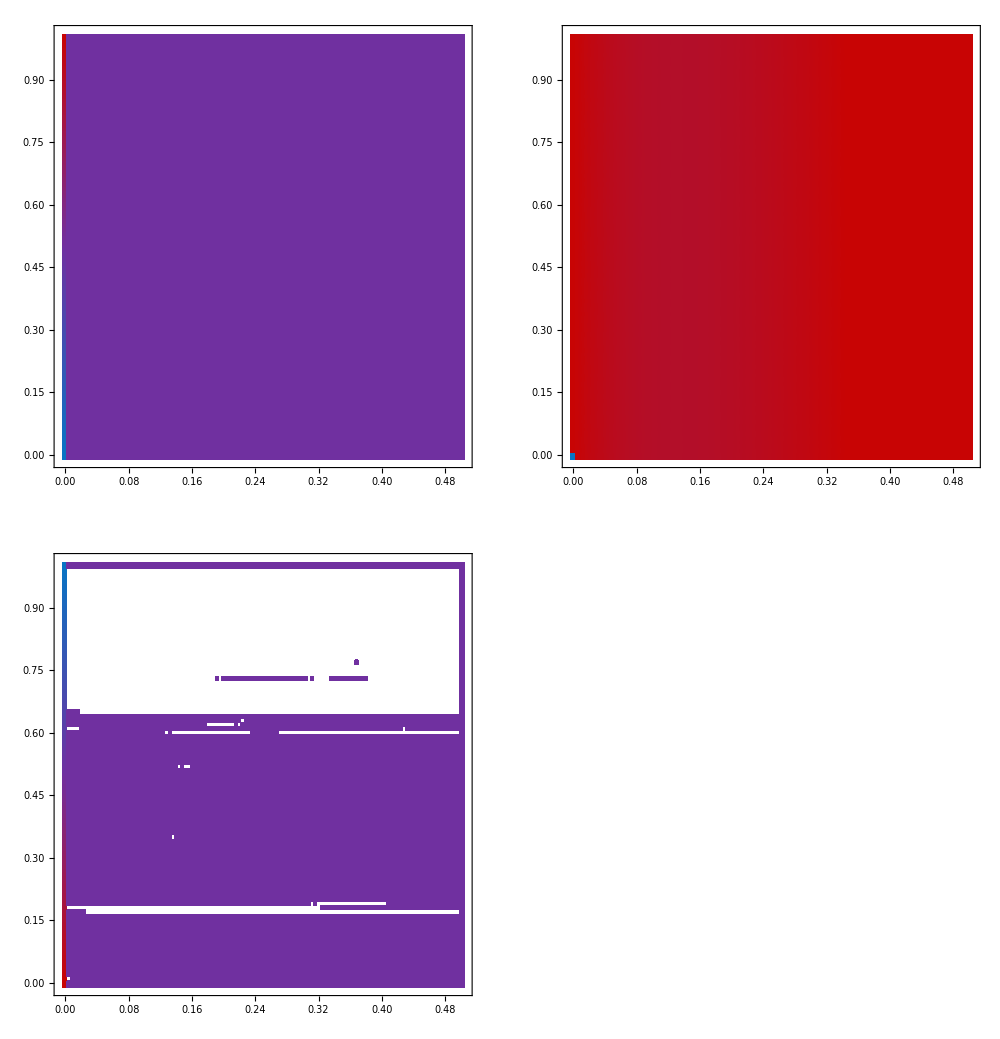
{-Graphics-Initial frequencyDispersal}

neutral_RMS.png

-Graphics-

{-Graphics-Initial frequencyDispersal}

neutral_RMS.png

neutral_RMS.png

```mathematica
PlotWFNasym[h10,(1-h10),h10,(1-h10),ΔwKK,ΔwKC,ΔwCK,ΔwCC,ΔvKK,ΔvKC,ΔvCK,ΔvCC,0.5,0.004]
Export["dummy.png",%];
b=Import["dummy.png"];

text={Graphics[Text[Style["a)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["b)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["c)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["d)",Directive[FontSize->12],FontFamily->"Times",FontColor-> Black]]]};
panels={Scaled[{0.1,0.94}],Scaled[{0.5,0.94}],Scaled[{0.1,0.53}],Scaled[{0.5,0.53}]};
c=ImageCompose[b,text,panels]
Export["neutral_RMS.png",c]
```

```mathematica
PlotWFNasym[h10,h10,(1-h10),(1-h10),ΔwKK,ΔwKC,ΔwCK,ΔwCC,ΔvKK,ΔvKC,ΔvCK,ΔvCC,0.5,0.004]
Export["dummy.png",%];
b=Import["dummy.png"];

text={Graphics[Text[Style["a)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["b)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["c)",Directive[FontSize-> 12],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["d)",Directive[FontSize->12],FontFamily->"Times",FontColor-> Black]]]};
panels={Scaled[{0.1,0.94}],Scaled[{0.5,0.94}],Scaled[{0.1,0.53}],Scaled[{0.5,0.53}]};
c=ImageCompose[b,text,panels]
Export["neutral_GMM.png",c]
```

## Analysis when one species evolves neutrally:

ΔV1H1 and ΔV2H2 are parameters:

```mathematica
Clear[ΔV1H1]
Clear[ΔV2H2]
```

```mathematica
S1d=s1*(1-s1)*(ΔV1H1)+ds*s2-ds*s1;
S2d=s2*(1-s2)*(ΔV2H2)-ds*s2+ds*s1;
```

Equilibria:

```mathematica
J=Simplify[{
{D[S1d,s1],D[S2d,s1]},{D[S1d,s2],D[S2d,s2]}}]//Simplify
```

{{-ds+ΔV1H1-2 s1 ΔV1H1,ds},{ds,-ds+ΔV2H2-2 s2 ΔV2H2}}

```mathematica
eqlist=Solve[{S1d,S2d}==0,{s1,s2}]//FullSimplify
```

{{s1→0,s2→0},{s1→1,s2→1},{s1→(ΔV1H1 (-2 ds+ΔV1H1) ΔV2H2-√(ΔV1H1^3 ΔV2H2 (-4 ds^2+ΔV1H1 ΔV2H2)))/(2 ΔV1H1^2 ΔV2H2),s2→(ΔV1H1^2 (-2 ds+ΔV2H2)+√(ΔV1H1^3 ΔV2H2 (-4 ds^2+ΔV1H1 ΔV2H2)))/(2 ΔV1H1^2 ΔV2H2)},{s1→(ΔV1H1 (-2 ds+ΔV1H1) ΔV2H2+√(ΔV1H1^3 ΔV2H2 (-4 ds^2+ΔV1H1 ΔV2H2)))/(2 ΔV1H1^2 ΔV2H2),s2→1/2-ds/ΔV2H2-(√(ΔV1H1^3 ΔV2H2 (-4 ds^2+ΔV1H1 ΔV2H2)))/(2 ΔV1H1^2 ΔV2H2)}}

```mathematica
stabilitytable=Table[J/.eqlist[[i]]//Eigenvalues//FullSimplify,{i,eqlist//Length}];
```

Stability of boundary equilibria:

```mathematica
stabilitytable[[1]]
```

{1/2 (-2 ds+ΔV1H1-√(4 ds^2+(ΔV1H1-ΔV2H2)^2)+ΔV2H2),1/2 (-2 ds+ΔV1H1+√(4 ds^2+(ΔV1H1-ΔV2H2)^2)+ΔV2H2)}

```mathematica
stabilitytable[[2]]
```

{1/2 (-2 ds-ΔV1H1-√(4 ds^2+(ΔV1H1-ΔV2H2)^2)-ΔV2H2),1/2 (-2 ds-ΔV1H1+√(4 ds^2+(ΔV1H1-ΔV2H2)^2)-ΔV2H2)}

Approximate internal equilibria:

```mathematica
assumptionfn[x_] := x/.{ds-> ds*ϵ,s1->s10+s11* ϵ, s2->s20+s21* ϵ};
{S1d,S2d}//assumptionfn//Factor;
Series[%,{ϵ,0,0}]//Normal(*0th Order Approximation*);
ans=Solve[%==0,{s10,s20}]//FullSimplify
```

{{s10→0,s20→0},{s10→1,s20→0},{s10→0,s20→1},{s10→1,s20→1}}

```mathematica
ApproximatedEq={};
Do[{sys={S1d,S2d}//assumptionfn//Factor;
exp=Series[sys,{ϵ,0,1}]//Normal(*First Order Approximation*);
eval=exp/.ans[[i]]//Factor;
firstorder=Solve[eval==0,{s11,s21}]//Factor;
approximated={};
Do[eqi=ans[[ i,j,2]]+firstorder[[1,j,2]];
AppendTo[approximated,eqi],{j,1,2}];
AppendTo[ApproximatedEq,approximated]},{i,1,Length[ans]}]
```

```mathematica
ApproximatedEq
```

{{0,0},{1-ds/ΔV1H1,-ds/ΔV2H2},{-ds/ΔV1H1,1-ds/ΔV2H2},{1,1}}

Approximate stability conditions:

```mathematica
StabilityofEQ[EQ_]:={
EQ//Simplify,
JC = J/.{s1-> EQ[[1]],s2->EQ[[2]]}/.{ds->ds ϵ,dh-> dh*ϵ};
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]//Factor;
Othorderλs,
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstsp=Table[{
λ11=a/.Othorderλs[[i]];
Solve[λ11==0,λ1]//Chop//Factor},{i,1,2}];
unsolvedfirstO=Table[{
λ11=a/.Othorderλs[[i]]//Chop//Factor},{i,1,2}];
firsts=firstsp//Flatten;
firsts//Factor//FullSimplify,
approximatedeigval=Othorderλs[[1;;2,1,2]]+firsts[[1;;2,2]]//Factor}
```

First internal equilibrium, final term in list is approximate stability criteria, stable when negative.

```mathematica
StabilityofEQ[ApproximatedEq[[2]]]
```

{{1-ds/ΔV1H1,-ds/ΔV2H2},{{λ0→-ΔV1H1},{λ0→ΔV2H2}},{λ1→ds,λ1→ds},{ds-ΔV1H1,ds+ΔV2H2}}

Second internal equilibrium. final term in list is approximate stability criteria, stable when negative.

```mathematica
StabilityofEQ[ApproximatedEq[[3]]]
```

{{-ds/ΔV1H1,1-ds/ΔV2H2},{{λ0→ΔV1H1},{λ0→-ΔV2H2}},{λ1→ds,λ1→ds},{ds+ΔV1H1,ds-ΔV2H2}}